```mathematica
nowarmup=False;
```

```mathematica
On[Assert];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SolarRadiation[J_,t_,ϕ_]:= Module[{result,S0=1.361,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];
cosψ[ti_]:=Sin[ϕ DtoR]sinδ + Cos[ϕ DtoR] cosδ Cos[(15.(ti-12))DtoR];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
tset = 12 + hs[δ]/15;

If[t< trise || t > tset, 
result = 0,
result = S0 cosψ[t];
];
result *= 1000;
result];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SunRise[J_,ϕ_]:= Module[{result,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
result= Re@trise;
result];

(*Fixed constant and solar radiation function *)
day = 72; lat = 30 ;
trise = SunRise[day,lat];ZZ= {0.01,0.1,1,5};

(* data for solar radiation *)
predata = Table[{t, SolarRadiation[day,t,lat]},{t, trise,trise+12,12/10}];
SR = Interpolation[predata];

th = 1.75; fs  =20;

ps = {{Gray,AbsoluteThickness[th]},{Dashed,Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[2 th]}};

as = Directive[AbsoluteThickness[th-1],fs,Black,FontFamily->"Arial"];
```

```mathematica
(*CONSTANTS AND SIMPLE FUNCTIONS USED*)

Ek =  7541; (*This is the ratio between E and k*)
c0= 28.;
c1 = 1.5;
cz = 0.5;

(*Convection*)
cp =29.3; (*J/ mol K*)
wind = 1; (*m/s*)
(*original data tissue density:
1 kg /l =  1 kg/dm^3 = 1000g/dm^3 = 1000 g/ 10^(-3) m^3  = 1 10^6 g/m^3
*)
δ = 0.15 10^(6);(*measurement gives the 0.15. g/m^3*)
Ksth =0.05* cp (*this is tissue conductance. A sleeping bag has 0.05 (ex #6.4, mol / m2 s * J / mol K  *);

s = 3.3472 ;(*specific heat capacity, 0.8 cal /g C = 0.8*4.184 J/g C*)
σ=5.67 10^(-8);(*W/m2 K4 = J / m2 s K*)
e = 0.04184;(*energy per contraction: 0.01 cal/g = 0.01*4.184 j/g*)

rK1 = 1; (* Coefficient for the conductance between the thorax and the rest of the body *)
rK2 = 1; (* Coefficient for the convection between the thorax and the environment *)
free = 0; (* Binary value 0 or 1 where there is free convection or laminar convection*)

Kv[z_]:= cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (* J/mol K x mol /m2 s = J / m2 K s*);

aw = 0.25; (*something per second*)
f[T_]:= aw T;

(*Start from radius calculating it is easier *)
rad[z_]:= (3. z/(2 π δ))^(1/3);
ch = 1; (*ch is the proportion of the cap with respect to the radius. radius * ch gives the height*)
h[z_]:= rad[z]* ch; (*The height of the cap*) 

(*ratio between thoracic and total mass*)
(*fcz[z_] := ((1/(3 2)) π h[z]^2  (3 rad[z] - h[z]))/(2/3 π r^3);*)
fcz[z_] := ((1/4)  h[z]^2  (3 rad[z] - h[z]))/(rad[z]^3);

(*Total surface of the spherical cap = surface of the thorax*)
Ath[z_]:= π rad[z] h[z] +  2 rad[z]^2 ArcCos[(rad[z]- h[z])/rad[z]] - (rad[z]-h[z])Sqrt[2 rad[z] h[z] - h[z]^2](*the first part is divided by 2 because of half a sphere, from pytagorian the base is a = (h (2 r - h))^(1/2) note that *)

(*Total surface are of  rest *)
As[z_]:= ( 2 π rad[z]^2  -  π rad[z] h[z] )  +   π rad[z]^2 (* m2*);

(*function for changes in environmental temperature*)
fTemp[t_,trise_,Trise_,Tmax_]:= Module[{tmax,tset,Tnoon,Tset,cT = 0.5,result},

If[
Trise == Tmax,result = Trise;Goto["end"]
];
Assert[Tmax >Trise];

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

result = 
Which[
trise≤ t< tmax,
 Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) t,
tmax ≤ t< tset,
 Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) t,
tset ≤ t< trise +24,
 Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)t
];

Label["end"];

result];

(*this function solve the the change in thoracic (and surface) temperature and find the warm-up time *)
Wtime[z_, rK1_, rK2_,starttf_,endtf_,free_, trise_, Trise_, Tmax_]:= Module[{ ε= 0.95, r3 =0.5,sol, cz = fcz[z], T1 , xy,pos,result, activetemp = c0 + c1 z cz ,Temp, newendtf, yy,maxyy,t1,t2,yt1,yt2,tmid,ytmid},

Temp[t_]:= fTemp[t,trise,Trise, Trise + Tmax ]; (*Simplify the definition of changes in temperature*)

T1 = Temp[starttf];
Assert[NumericQ@T1 == True];
newendtf = Min[endtf,12  +  (12 -trise)];

If[T1 ≥ activetemp, result = 0.; Goto[end]];

sol = If[free == 0,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (0. * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05Max[0.,(Ts[t]- Temp[t/3600.])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3  SR[t/3600.])) ,Tth[starttf*3600.]==Ts[starttf*3600.]==T1},{Tth,Ts},{t,starttf *3600., newendtf* 3600.}],
NDSolve[
{Tth'[t] == 1/(s cz z) (0. * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Temp[t/3600.]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3 SR[t/3600.])) ,Tth[starttf*3600.]==Ts[starttf*3600.]==T1},{Tth,Ts},{t,starttf *3600.,newendtf *3600.}]
];


(* Compute all values *)
yy = Table[Evaluate[Re@Tth[t]/.sol],{t,starttf*3600,newendtf*3600,2}];
maxyy = Max[yy];

If[maxyy < activetemp,
result = endtf -starttf,
pos = Position[yy,maxyy][[1,1]];
t1 = starttf*3600;
t2 = t1 + 2(pos-1); (*The minus one occurs because imagine max is at starttf, time 2 because of discretization in yy*)
yt1 = Evaluate[Re@Tth[t1] /. sol][[1]] - activetemp;
yt2 = Evaluate[Re@Tth[t2] /. sol][[1]] -activetemp;
Assert[yt1*yt2 < 0];
While[Abs[yt1 -yt2] > 10^(-5),
tmid = t1 + (t2 -t1)/2;
ytmid = Evaluate[Re@Tth[tmid] /. sol][[1]] - activetemp;
If[ytmid < 0,
t1 = tmid;
yt1 = ytmid,
t2 = tmid;
yt2 = ytmid
];
];
result = (t1 + t2)/(2. 3600) - starttf;
];
Label[end];
result];
```

```mathematica
(*Functions for resting, active and foraging rate*)
(* Multiply by  3600 to convert from second to hour*)
(* The unit is  in Watt hour = joule/hour*)

(* Resting metabolic rate per hour*)
eb[z_, T_, a1_, b1_]:= 3600. a1 z^b1 Exp[(- Ek)/(T + 273.15)] 10^8; (*COMPARE WITH Niven JE,Scharlemann JP.Do insect metabolic rates at rest and during flight scale with body mass?Biology Letters.2005;1(3):346-349. doi:10.1098/rsbl.2005.0311. *)

(* Active metabolic rate*)
ea[z_, T_, a2_, b2_]:= 3600. a2 z^b2 Exp[(- Ek)/Max[c0  + c1 z cz, T + 273.15]] 10^8;

(* Foraging rate*)
eg[z_, a3_,b3_,ε_:16]:= ε a3 z^b3 10 ;  (* use this so that in 60 min they take about 10  times their body mass if b3 = 1, ε = 4 cal/g = 16 J/g*)
```

Those values are just to get thing within one range of magnitude. This now matches with the appendix data from 1 

278.93 * 10^(-3) * 20 //ScientificForm (* 300 mm3/O2 h x 10^(-3) ml x 20  (O2 5 x 4. to cal to joule)  *) 

(* this is in watt *)
eb[5.165,23,1,0.75]  //ScientificForm

Let us assume that an insect can not take more than 250 times its mass.
C. humectus hidalgoensis is has a mean of 0.18 g and move 1.19 g during 23 min = 23/60 = 0.38 hour , then

1	Niven JE, Scharlemann JP. Do insect metabolic rates at rest and during flight scale with body mass? Biology Letters. 2005;1(3):346-349. doi:10.1098/rsbl.2005.0311.

```mathematica
Eb[z_,trise_, Trise_, Tmax_, tstart_, tend_, abparam_]:= Module[{ tset,Tnoon, Tset,tstart1,tend1, tstart2, tend2, tstart3,tend3,I1, I2, I3, result1= 0, result2 = 0, result3 = 0,f1,f2,f3,a1 , b1 , tmax,cT = 0.5,result},

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

a1 = abparam[[1]];
b1 = abparam[[2]];

(* Due to the piecewise nature of temperature I need to break it down into 3 pieces *)
Assert[tstart≥ trise];

I1 = IntervalIntersection[Interval[{trise, tmax}],Interval[{tstart,tend}]];
I2 =  IntervalIntersection[Interval[{tmax,tset}],Interval[{tstart,tend}] ];
I3 =  IntervalIntersection[Interval [{tset, trise +24}],Interval[{tstart,tend}] ];

If[Length[I1]≠ 0,
tstart1 = I1[[1,1]];
tend1 = I1[[1,2]];
];

If[Length[I2]≠ 0,
tstart2 = I2[[1,1]];
tend2 = I2[[1,2]];
];

If[Length[I3]≠ 0,
tstart3 = I3[[1,1]];
tend3 = I3[[1,2]];
];

f1 = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) # &;

If[tstart1< tend1,
result1 = NIntegrate[eb[z, f1[t],a1,b1],{t,tstart1, tend1}]
];

f2 = Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) # &; 
If[tstart2< tend2,
result2 = NIntegrate[eb[z, f2[t],a1,b1],{t,tstart2, tend2}]
];

f3= Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)# &;
If[tstart3< tend3,
result3 = NIntegrate[eb[z, f3[t],a1,b1],{t,tstart3, tend3}]
];

result = result1 + result2+ result3;

result];

Ea[z_,trise_, Trise_, Tmax_, tstart_, tend_,abparam_]:= Module[{tset,Tnoon, Tset,tstart1=0,tend1=0, tstart2=0, tend2=0, tstart3=0,tend3=0,I1, I2, I3, result1= 0, result2 = 0, result3 = 0,f1,f2,f3,a2 , b2, tmax,cT = 0.5,result},

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

a2 = abparam[[1]];
b2 = abparam[[2]];


(* Due to the piecewise nature of temperature I need to break it down into 3 pieces *)
Assert[tstart≥ trise];
(* Due to the piecewise nature of temperature I need to break it down into 3 pieces *)
Assert[tstart≥ trise];

I1 = IntervalIntersection[Interval[{trise, tmax}],Interval[{tstart,tend}]];
I2 =  IntervalIntersection[Interval[{tmax,tset}],Interval[{tstart,tend}] ];
I3 =  IntervalIntersection[Interval [{tset, trise +24}],Interval[{tstart,tend}] ];

If[Length[I1]≠ 0,
tstart1 = I1[[1,1]];
tend1 = I1[[1,2]];
];

If[Length[I2]≠ 0,
tstart2 = I2[[1,1]];
tend2 = I2[[1,2]];
];

If[Length[I3]≠ 0,
tstart3 = I3[[1,1]];
tend3 = I3[[1,2]];
];

f1 = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) # &;

If[tstart1< tend1,
result1 = NIntegrate[ea[z, f1[t],a2,b2],{t,tstart1, tend1}]
];

f2 = Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) # &; 
If[tstart2< tend2,
result2 = NIntegrate[ea[z, f2[t],a2,b2],{t,tstart2, tend2}]
];

f3= Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)# &;
If[tstart3< tend3,
result3 = NIntegrate[ea[z, f3[t],a2,b2],{t,tstart3, tend3}]
];

result = result1 + result2+ result3;

result];

(*When resource is limiting, compute tstart and tend first*)
tf[z_,RR_,a3_,b3_]:= RR/(a3 z^b3 10);

Eg[z_,ε_,tstart_,tend_,abparam_]:= Module[{a3, b3,result},
a3 = abparam[[1]];
b3= abparam[[2]];

result = (tend -tstart) eg[z,a3,b3, ε];
result];
```

```mathematica
(* Energy budget given time is limited *)
En[z_,trise_, Trise_, Tmax_, ε_, starttf_, tf_, allabparam_]:= Module[{result =0., gain= 0., activity = 0.,rest = 0.,tstart1,tend1,tstart2,tend2, abparam1,abparam2,abparam3,finaltf, newstarttf, warmtime},

abparam1= allabparam[[{1,2}]];
abparam2= allabparam[[{3,4}]];
abparam3= allabparam[[{5,6}]];

(* Calculate the amount of time needed to warm-up, the subtract witht total foraging time tf *)
(*Print["Trise_",Trise];*)
warmtime = Wtime[z, rK1,rK2, starttf,starttf+tf,free,trise,Trise,Tmax];
Assert[NumericQ[warmtime]==True];
(*Print["End_Trise"];
*)
If[nowarmup==True,warmtime=0];

If[warmtime ≥ tf, 
result = - Eb[z,trise,Trise, Tmax, trise, trise+24,abparam1];Goto[here];
];

newstarttf = starttf + warmtime;

finaltf = Min[starttf + tf,trise+24] ;
Assert[trise ≤ starttf];

(*Total energy gained*)
gain = Eg[z, ε, newstarttf, finaltf, abparam3];

(*Total energy used for activity*)
activity = Ea[z,trise,Trise, Tmax, newstarttf,finaltf,abparam2];

(*Total energy for resting*)
If[trise == newstarttf, (*the individual will rest until the rest of the day after foraging*)
rest = Eb[z,trise,Trise, Tmax, finaltf, trise + 24 , abparam1], (* otherwise, it will rest until starttf *)
tstart1 = trise;
tend1 = newstarttf;
rest = Eb[z,trise,Trise, Tmax, tstart1, tend1,abparam1];
If[starttf +tf < trise + 24,
tstart2 = starttf + tf;
tend2 = trise + 24;
rest += Eb[z,trise,Trise, Tmax, tstart2, tend2,abparam1];
];
];
result = gain - activity - rest;

Label[here];(*If warm-up takes longer than total foraging time allowed tf *)

result];
```

## No warm-up

### Figure for showing the influence of b3, no warmup, fixed temperature: don’t forget to switch of warm-up by making nowarmup = False

```mathematica
a1 = 1; b1 = 0.75; a2 = 10 a1; b2 = 0.75;  a3 = 1; b3 = 0.75;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
```

#### This is when time is limiting

```mathematica
Fig = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)


Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig,fig];
,{cTmax,{0}},{startforaging,{trise}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5,0.75,1}},{tf,{1}}];
```

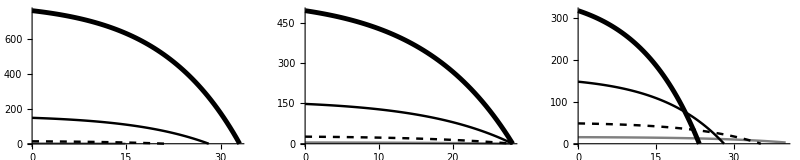

```mathematica
d1 =GraphicsRow[Reverse@Fig,ImageSize->800]
```

```mathematica
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig4a.jpg",d1, ImageResolution->100];
```

#### This is when resource is limiting

```mathematica
Fig = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  = Table[Min[tf[ZZ[[i]], RR, a3,b3],tf[ZZ[[i]],ZZ[[i]]*250 , a3,b3]],{i,4}]; (* in hour*)

Do[
f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,foragingduration[[i]],allabparam];

fig = Plot[{f[temp,1],f[temp,2],f[temp,3],f[temp,4]}, {temp,0,40},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];

AppendTo[Fig,fig];
,{cTmax,{0(*, 5, 10, 15,25*)}},{startforaging,{trise(*, 2 12 - trise, 12, 12 + 0.5 (12 -  trise)*)}}];
(*
p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];

Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\fig_b3_"<>ToString@b3<>"_R_"<>ToString@RR<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5,0.75,1}},{RR,{5}}];
```

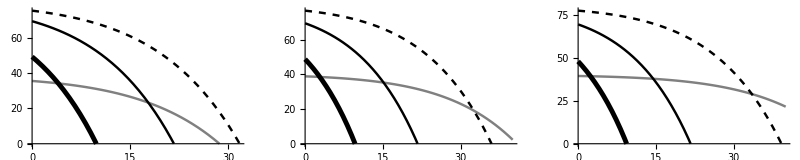

```mathematica
d1 =GraphicsRow[Reverse@Fig,ImageSize->800]
```

```mathematica
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig4b.jpg",d1, ImageResolution->100];
```

## With warm-up

### Free convection

#### Default panel + late foraging

```mathematica
ZZ= {0.01,0.1,1,10};
Fig = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig,fig];
,{cTmax,{0}},{startforaging,{trise, trise+3}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5}},{tf,{2}}];
```

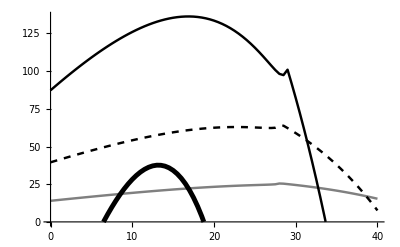
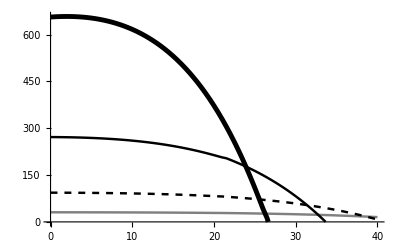

```mathematica
Fig
```

#### For proposal: Default panel + late foraging

```mathematica
th = 1.25; fs  =12;

ps = {{Gray,AbsoluteThickness[th]},{Dashed,Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th/2]},{Black,AbsoluteThickness[1.5 th]}};

as = Directive[AbsoluteThickness[0.75],fs,Black,FontFamily->"Arial"];
```

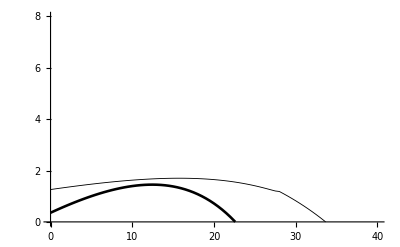
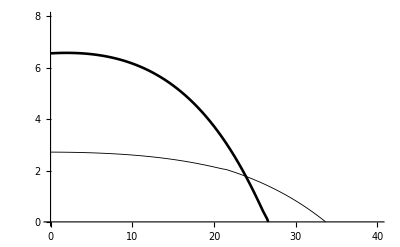
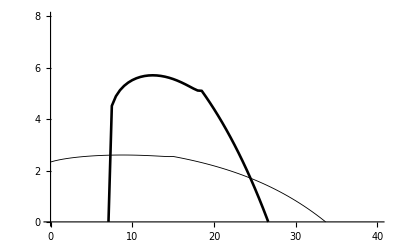

```mathematica
ZZ= {0.01,0.1,1,10};
Fig = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1.25; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
(*data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];*)
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{(*data1,data2,*)data3,data4},PlotRange->{{0,40},{0,800}},AxesOrigin-> {0,0},PlotStyle->ps[[3;;]],AxesStyle-> as,PlotRangePadding->None,Ticks->{{0,10,20,30,40},{{0,0},{200,2},{400,4},{600,6},{800,8}}}];
AppendTo[Fig,fig];
,{cTmax,{0}},{startforaging,{trise+0.25, trise+3,trise+10}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5}},{tf,{2}}];Fig
```

```mathematica
Export["C:\\Users\\Tanjona\\Documents\\energy_budget\\ms_fig\\proposal_fig.pdf",GraphicsRow[Fig,Spacings->-20]]
```

C:\Users\Tanjona\Documents\energy_budget\ms_fig\proposal_fig.pdf

#### Long foraging

```mathematica
ZZ= {0.01,0.1,1,10};
Fig2 = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig2,fig];
,{cTmax,{0}},{startforaging,{trise}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5}},{tf,{4}}];
```

#### Increase cTmax

```mathematica
ZZ= {0.01,0.1,1,10};
Fig3 = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig3,fig];
,{cTmax,{10}},{startforaging,{trise}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5}},{tf,{2}}];
```

#### Increase b3

```mathematica
ZZ= {0.01,0.1,1,10};
Fig4 = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig4,fig];
,{cTmax,{10}},{startforaging,{trise}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.75}},{tf,{2}}];
```

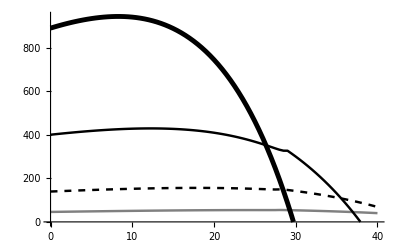
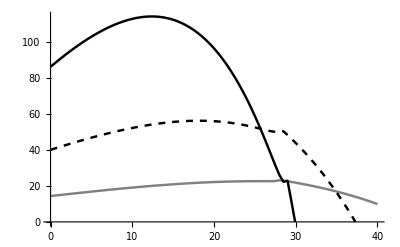
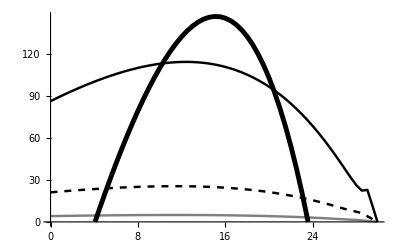
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FIG = Flatten[{Fig,Fig2,Fig3,Fig4}]
```

```mathematica
text= {"default","late_warmup","long_foraging","variable_temp","high_b3"};
Do[
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig5_free_"<>text[[i]]<>".jpg",FIG[[i]],ImageResolution->100];
,{i,5}];
```

### Laminar convection

#### Default panel + late foraging

```mathematica
ZZ= {0.01,0.1,1,10};
Fig = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig,fig];
,{cTmax,{0}},{startforaging,{trise+3, trise+6}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5}},{tf,{2}}];
```

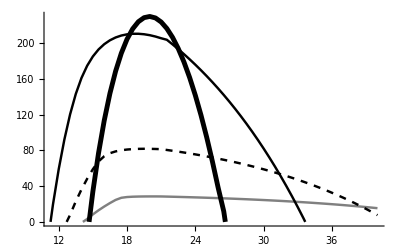
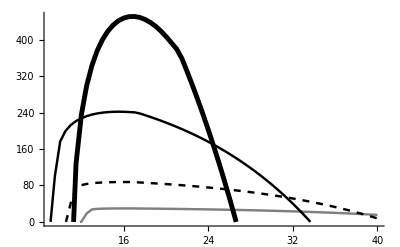

```mathematica
Fig
```

#### Long foraging

```mathematica
ZZ= {0.01,0.1,1,10};
Fig2 = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig2,fig];
,{cTmax,{0}},{startforaging,{trise+3}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5}},{tf,{4}}];
```

#### Increase cTmax

```mathematica
ZZ= {0.01,0.1,1,10};
Fig3 = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig3,fig];
,{cTmax,{10}},{startforaging,{trise+3}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.5}},{tf,{2}}];
```

#### Increase b3

```mathematica
ZZ= {0.01,0.1,1,10};
Fig4 = {};
Do[
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 16;
foragingduration  =1; (* in hour*)
Do[

f[Trise_,i_]:=En[ZZ[[i]], trise,Trise, Trise +cTmax,ε, startforaging,tf,allabparam];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,3]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,4]},{temp,0,40,step}];

fig = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None];
AppendTo[Fig4,fig];
,{cTmax,{10}},{startforaging,{trise+3}}];

(*p1 =GraphicsGrid[Transpose@Partition[Fig,4],ImageSize->1000];*)

(*Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\10 ms\\results\\n_fig_warm_"<>ToString@free<>"_b3_"<>ToString@b3<>"_tf_"<>ToString@tf<>".jpg",p1,ImageResolution->100];*)
,{b3,{0.75}},{tf,{2}}];
```

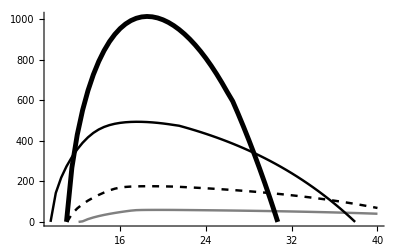
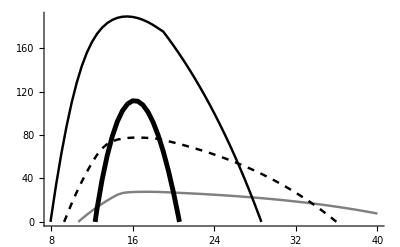
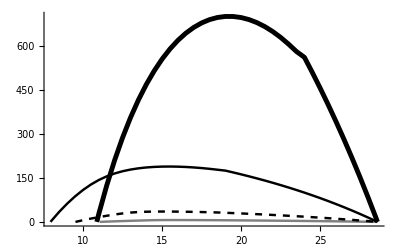
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FIG = Flatten[{Fig,Fig2,Fig3,Fig4}]
```

```mathematica
text= {"default","late_warmup","long_foraging","variable_temp","high_b3"};
Do[
Export["C:\\Users\\Tanjona\\Documents\\Projects\\1 Size and range\\ms_fig\\fig5_laminar_"<>text[[i]]<>".jpg",FIG[[i]],ImageResolution->100];
,{i,5}];
```